{{Null},{Null}}

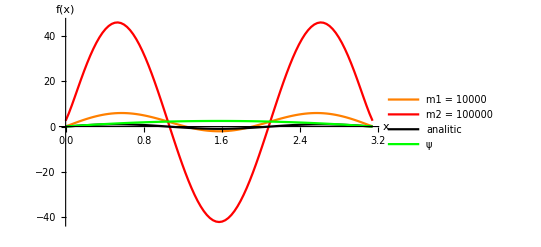

31.4262

```mathematica
{{m1= Import["C:\\GitHub\\metod_ustanovleniya\\m1.csv"];}, {m2= Import["C:\\GitHub\\metod_ustanovleniya\\m2.csv"];}}
(*tau = 0.00000001
h = 100/π
m1 = 10000
m2 = 100000*)
Sol= DSolve[{u''[x] + 9 Sin[3 x]==0 && u[0]==0&&u[π]==0},u[x],x]; 
SolF = (u[x]/.{Sol})[[1,1]];
ψ[x_] := x(π-x); ψplot = Plot[ψ[x],{x,0,π}, PlotStyle -> Green, PlotLegends-> {"ψ"}];
SolFPlot = Plot[SolF,{x,0,π}, PlotStyle -> Black,PlotLegends-> {"analitic"}];
plotm1 =ListLinePlot[m1, PlotStyle -> Orange,PlotLegends-> {"m1 = 10000"}];
plotm2 =ListLinePlot[m2, PlotStyle -> Red,PlotLegends-> {"m2 = 100000"}];
Show[plotm1, plotm2,SolFPlot, ψplot,PlotRange -> All, AxesLabel -> {"x","f(x)"}]
err = 0.;
For[i=1, i <= Length[m1], i++,
err += (m1[[i,2]]-(SolF/.{x->m1[[i,1]]}))^2;]
√err
```

```mathematica
m1[[1,2]]
```

0.112841

```mathematica
SolF/.{x->m1[[1,1]]}
```

0